## Note: In order for the following command to work, the package kColorConnectivity must be installed on your machine. Alternatively, you can open the .wl file and click, “run package” in the upper right corner of the file.

```mathematica
Needs["kColorConnectivity`"]
```

## Note: Scrolling over the function and selecting the arrow gives a brief description of usage, and suitable inputs.

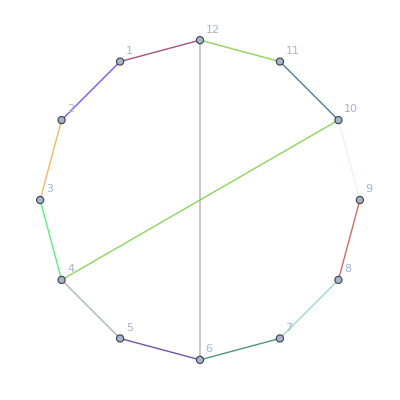
```mathematica
KPathAssociation[-Graphics-,8]
```

{Yes}

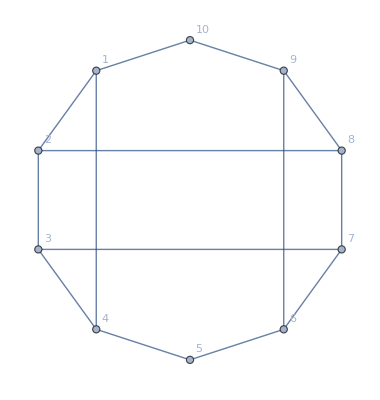
```mathematica
KPathAssociation[-Graphics-,8]
```

{Yes}

```mathematica
KColorExist[-Graphics-,8]
```

{Yes}

## Note: Using version 11 allows the user to click on a subset under the “Paths with k or more colors” column, see the input graph with intended paths highlighted, and have each be categorized by number of colors obtained.

```mathematica
KColorDataset[-Graphics-,8]
```

Dataset[<>]

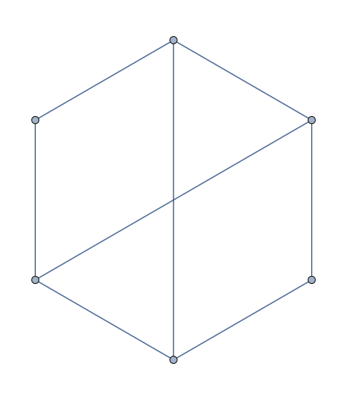

```mathematica
CompleteBipartiteEdgeAdder[6,{1,3},2,4]
```

## Note: For large graphs using a significant amount of chords, computation time can be in the range of hours.

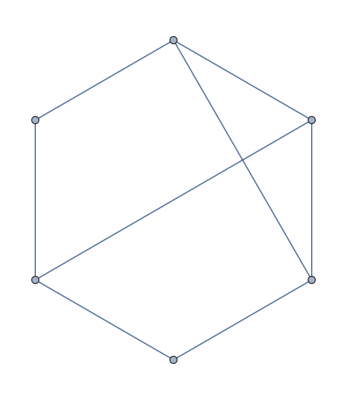
{-Graphics-,-Graphics-}

```mathematica
ChordedCycle[6,2,4]
```

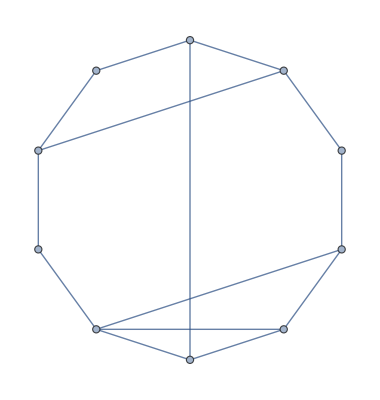
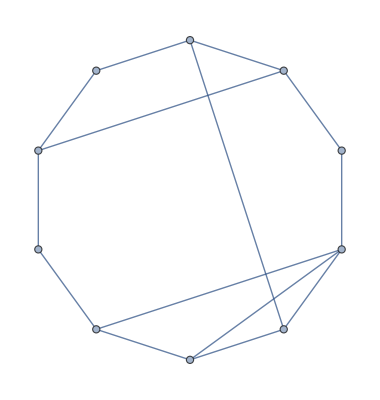
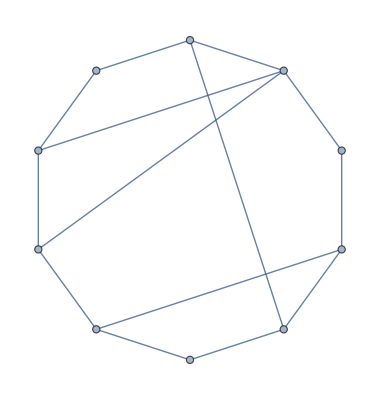
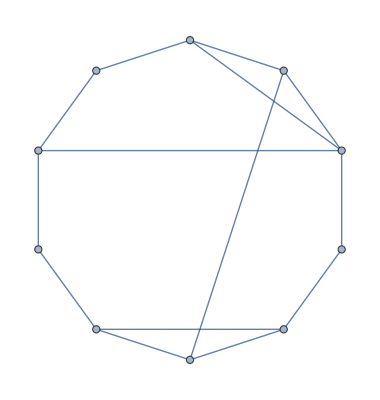
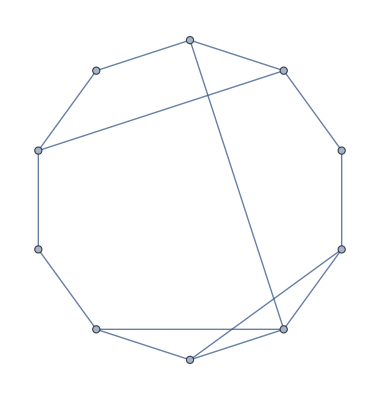
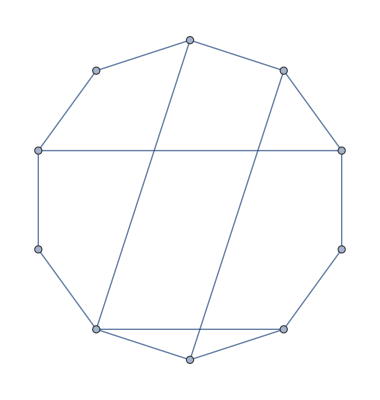
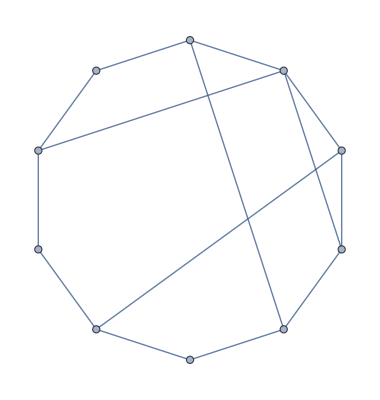
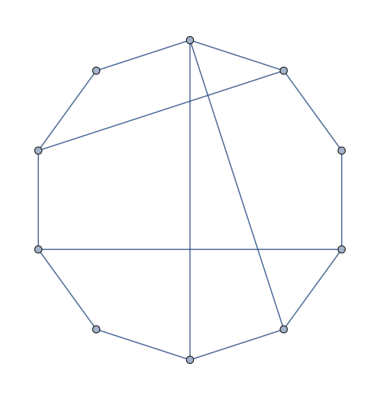

```mathematica
ChordedCycle[10,4,8]
```

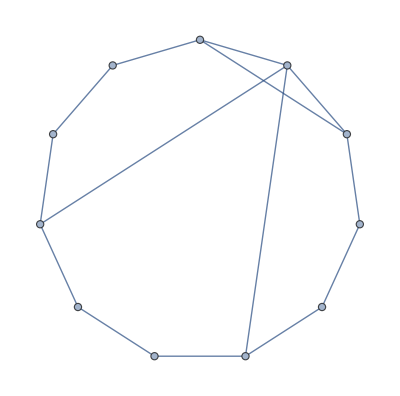
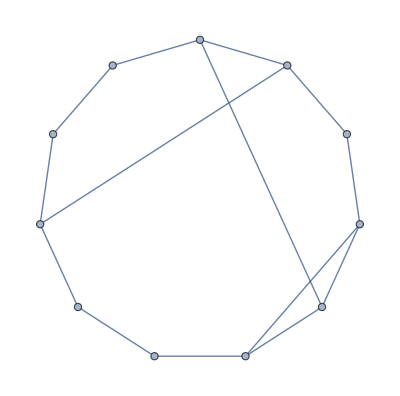
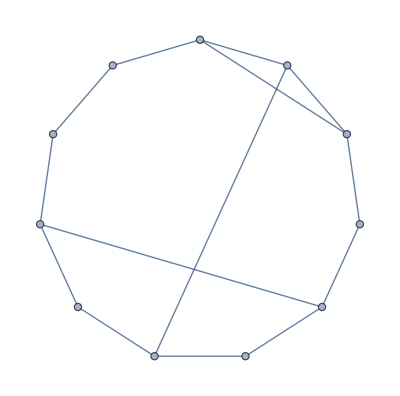
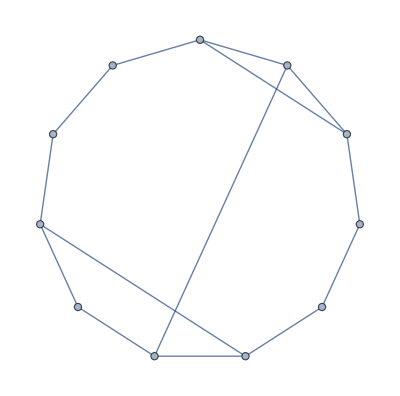
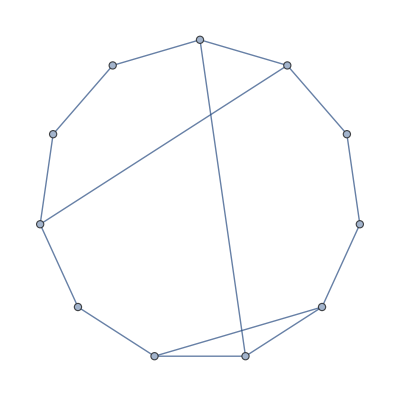
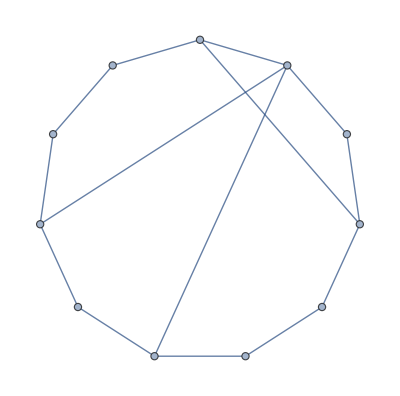
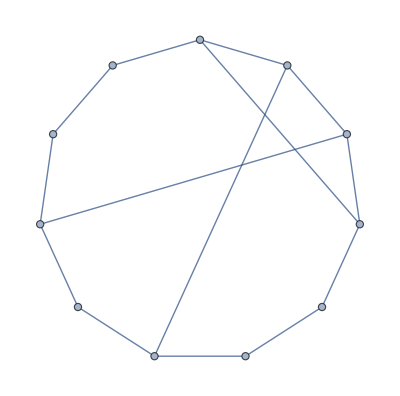
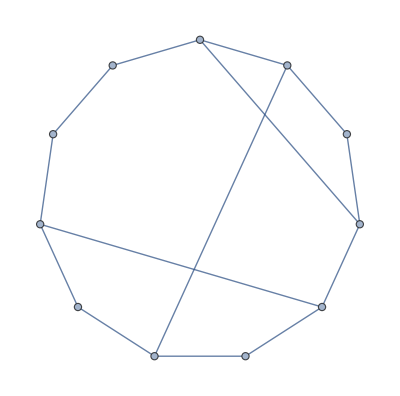

```mathematica
ChordedCycle[11,3,8]
```

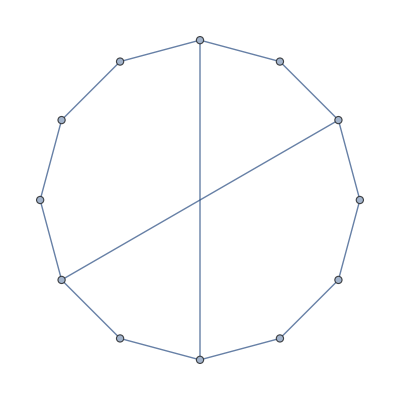

```mathematica
ChordedCycle[12,2,8]
```

## Note: Shows one of the graphs explored during Summer 2016, colors are chosen at random, although parallel chords are attributed the same color.

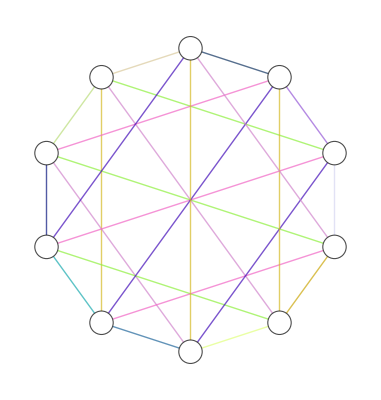

```mathematica
CompleteBipartiteEdgeColorer[10]
```

## A table of the same module.

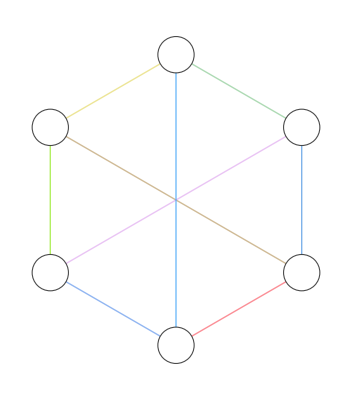
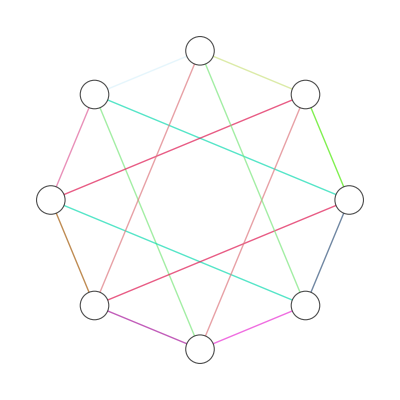
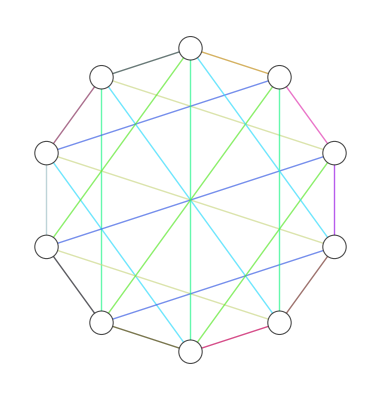
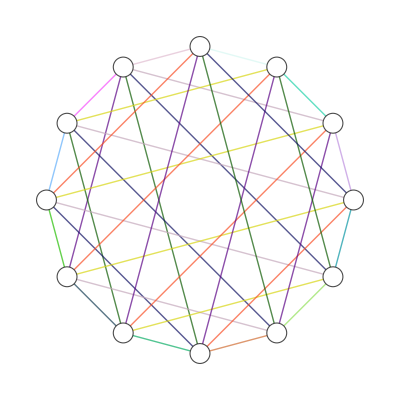
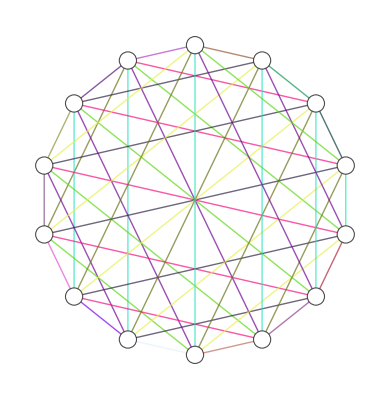
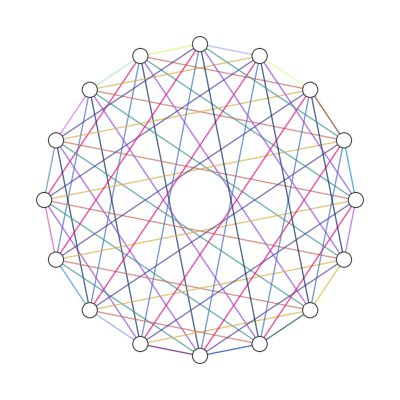
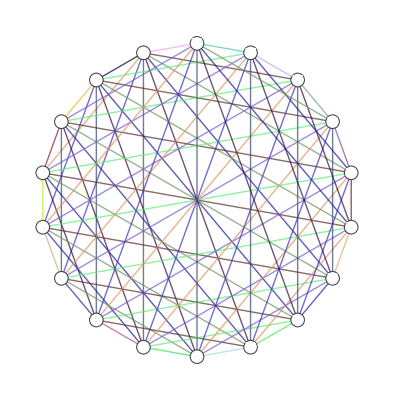
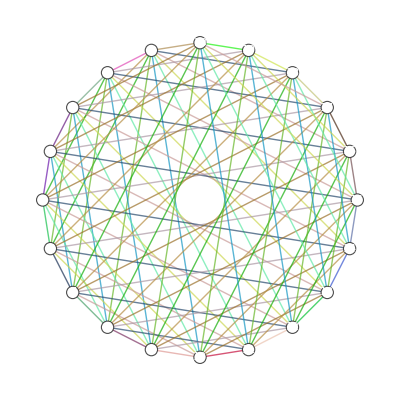

```mathematica
Table[CompleteBipartiteEdgeColorer[n],{n,6,20,2}]
```

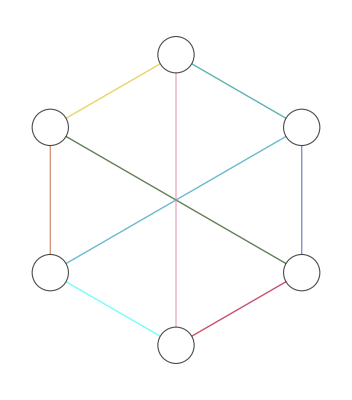
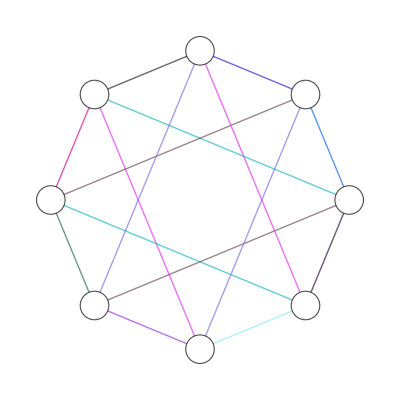
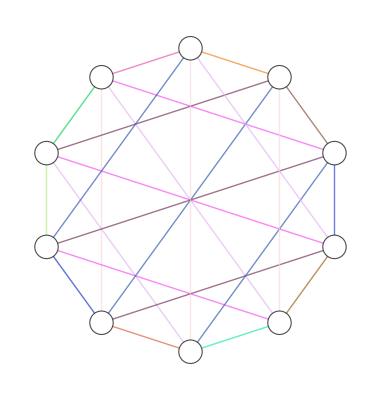
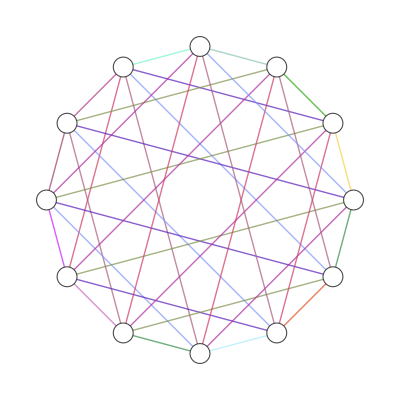
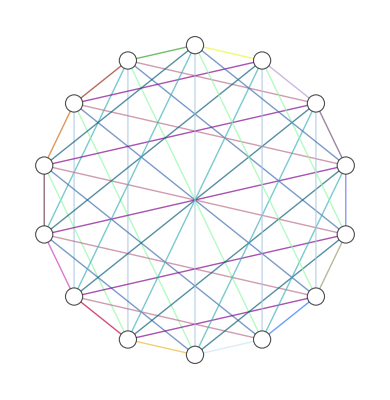
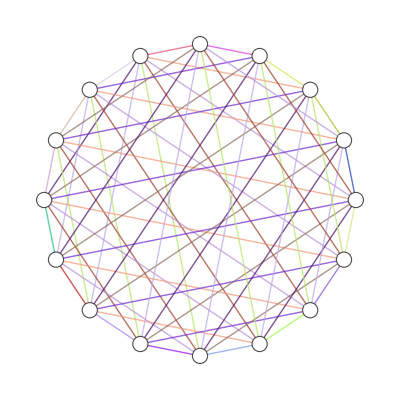
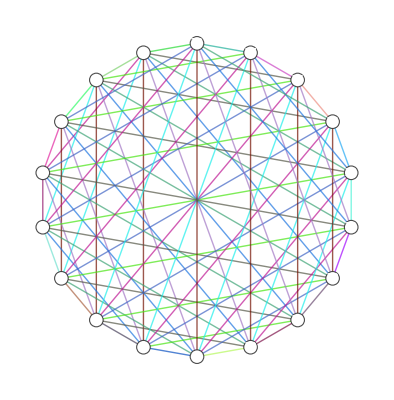
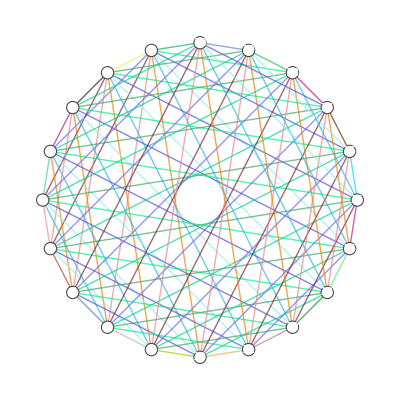

## Error Handling

```mathematica
CompleteBipartiteEdgeColorer[5]
```

Input must be an even number

$Aborted